```mathematica
mag
```

```mathematica
Clear[f,net,k,r,b]
```

```mathematica
<<toy2D`
```

```mathematica
Get["linearModel`"]
```

its alive

its alive

its alive

«4 more identical outputs»

```mathematica
annotatedTune[f_]:=(r=Range[-5,15,.1];Show[plot[datum~Join~Thread[{r,First[f@#]&/@r}]],Epilog->Text[error[f],{10,0.9},{-1,0}]])
```

## study nips, find out what is happening and find a supervisor!

```mathematica
net=NetInitialize[NetChain[{
(*Implicit LinearLayer[1]*) 
LinearLayer[1000],
Tanh,
LinearLayer[1000],
Ramp,


LinearLayer[1]
},"Input"->1]]
```

NetChain[<>]

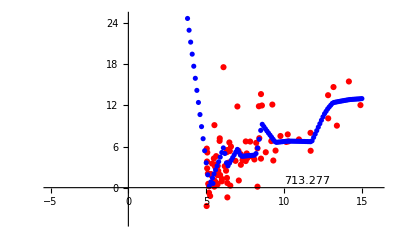

```mathematica
model=NetTrain[net,format/@datum,
Method->{"ADAM","LearningRate"->0.001},BatchSize->Length[datum],TargetDevice->{"GPU",3},
MaxTrainingRounds->Quantity[30,"Seconds"],TrainingProgressReporting->{Function[annotatedTune[#Net]],"Interval"->Quantity[1,"Seconds"]}];
annotatedTune[model]
```

```mathematica
ZZZ
```

Show::gtype: plot is not a type of graphics.

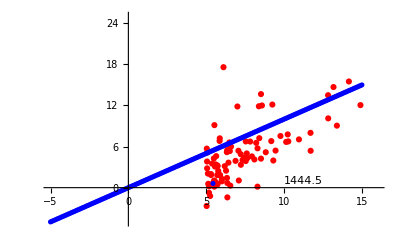

```mathematica
Show[plot[Join[datum,{{-5.,-5.},{-4.9,-4.9},{-4.8,-4.8},{-4.7,-4.7},{-4.6,-4.6},{-4.5,-4.5},{-4.4,-4.4},{-4.3,-4.3},{-4.2,-4.2},{-4.1,-4.1},{-4.,-4.},{-3.9,-3.9},{-3.8,-3.8},{-3.7,-3.7},{-3.5999999999999996,-3.5999999999999996},{-3.5,-3.5},{-3.4,-3.4},{-3.3,-3.3},{-3.2,-3.2},{-3.0999999999999996,-3.0999999999999996},{-3.,-3.},{-2.9,-2.9},{-2.8,-2.8},{-2.6999999999999997,-2.6999999999999997},{-2.5999999999999996,-2.5999999999999996},{-2.5,-2.5},{-2.4,-2.4},{-2.3,-2.3},{-2.1999999999999997,-2.1999999999999997},{-2.0999999999999996,-2.0999999999999996},{-2.,-2.},{-1.9,-1.9},{-1.7999999999999998,-1.7999999999999998},{-1.6999999999999997,-1.6999999999999997},{-1.5999999999999996,-1.5999999999999996},{-1.5,-1.5},{-1.4,-1.4},{-1.2999999999999998,-1.2999999999999998},{-1.1999999999999997,-1.1999999999999997},{-1.0999999999999996,-1.0999999999999996},{-1.,-1.},{-0.8999999999999995,-0.8999999999999995},{-0.7999999999999998,-0.7999999999999998},{-0.7000000000000002,-0.7000000000000002},{-0.5999999999999996,-0.5999999999999996},{-0.5,-0.5},{-0.39999999999999947,-0.39999999999999947},{-0.2999999999999998,-0.2999999999999998},{-0.1999999999999993,-0.1999999999999993},{-0.09999999999999964,-0.09999999999999964},{0.,0.},{0.10000000000000053,0.10000000000000053},{0.20000000000000018,0.20000000000000018},{0.3000000000000007,0.3000000000000007},{0.40000000000000036,0.40000000000000036},{0.5,0.5},{0.6000000000000005,0.6000000000000005},{0.7000000000000002,0.7000000000000002},{0.8000000000000007,0.8000000000000007},{0.9000000000000004,0.9000000000000004},{1.,1.},{1.1000000000000005,1.1000000000000005},{1.2000000000000002,1.2000000000000002},{1.3000000000000007,1.3000000000000007},{1.4000000000000004,1.4000000000000004},{1.5,1.5},{1.6000000000000005,1.6000000000000005},{1.7000000000000002,1.7000000000000002},{1.8000000000000007,1.8000000000000007},{1.9000000000000004,1.9000000000000004},{2.,2.},{2.1000000000000005,2.1000000000000005},{2.2,2.2},{2.3000000000000007,2.3000000000000007},{2.4000000000000004,2.4000000000000004},{2.5,2.5},{2.6000000000000005,2.6000000000000005},{2.7,2.7},{2.8000000000000007,2.8000000000000007},{2.9000000000000004,2.9000000000000004},{3.,3.},{3.0999999999999996,3.0999999999999996},{3.200000000000001,3.200000000000001},{3.3000000000000007,3.3000000000000007},{3.4000000000000004,3.4000000000000004},{3.5,3.5},{3.5999999999999996,3.5999999999999996},{3.700000000000001,3.700000000000001},{3.8000000000000007,3.8000000000000007},{3.9000000000000004,3.9000000000000004},{4.,4.},{4.1,4.1},{4.200000000000001,4.200000000000001},{4.300000000000001,4.300000000000001},{4.4,4.4},{4.5,4.5},{4.600000000000001,4.600000000000001},{4.700000000000001,4.700000000000001},{4.800000000000001,4.800000000000001},{4.9,4.9},{5.,5.},{5.100000000000001,5.100000000000001},{5.200000000000001,5.200000000000001},{5.300000000000001,5.300000000000001},{5.4,5.4},{5.5,5.5},{5.600000000000001,5.600000000000001},{5.700000000000001,5.700000000000001},{5.800000000000001,5.800000000000001},{5.9,5.9},{6.,6.},{6.100000000000001,6.100000000000001},{6.200000000000001,6.200000000000001},{6.300000000000001,6.300000000000001},{6.4,6.4},{6.5,6.5},{6.600000000000001,6.600000000000001},{6.700000000000001,6.700000000000001},{6.800000000000001,6.800000000000001},{6.9,6.9},{7.,7.},{7.100000000000001,7.100000000000001},{7.200000000000001,7.200000000000001},{7.300000000000001,7.300000000000001},{7.4,7.4},{7.5,7.5},{7.600000000000001,7.600000000000001},{7.700000000000001,7.700000000000001},{7.800000000000001,7.800000000000001},{7.9,7.9},{8.,8.},{8.100000000000001,8.100000000000001},{8.200000000000001,8.200000000000001},{8.3,8.3},{8.4,8.4},{8.5,8.5},{8.600000000000001,8.600000000000001},{8.700000000000001,8.700000000000001},{8.8,8.8},{8.9,8.9},{9.,9.},{9.100000000000001,9.100000000000001},{9.200000000000001,9.200000000000001},{9.3,9.3},{9.4,9.4},{9.5,9.5},{9.600000000000001,9.600000000000001},{9.700000000000001,9.700000000000001},{9.8,9.8},{9.9,9.9},{10.,10.},{10.100000000000001,10.100000000000001},{10.200000000000001,10.200000000000001},{10.3,10.3},{10.4,10.4},{10.5,10.5},{10.600000000000001,10.600000000000001},{10.700000000000001,10.700000000000001},{10.8,10.8},{10.9,10.9},{11.,11.},{11.100000000000001,11.100000000000001},{11.2,11.2},{11.3,11.3},{11.400000000000002,11.400000000000002},{11.5,11.5},{11.600000000000001,11.600000000000001},{11.7,11.7},{11.8,11.8},{11.900000000000002,11.900000000000002},{12.,12.},{12.100000000000001,12.100000000000001},{12.2,12.2},{12.3,12.3},{12.400000000000002,12.400000000000002},{12.5,12.5},{12.600000000000001,12.600000000000001},{12.7,12.7},{12.8,12.8},{12.900000000000002,12.900000000000002},{13.,13.},{13.100000000000001,13.100000000000001},{13.2,13.2},{13.3,13.3},{13.400000000000002,13.400000000000002},{13.5,13.5},{13.600000000000001,13.600000000000001},{13.7,13.7},{13.8,13.8},{13.900000000000002,13.900000000000002},{14.,14.},{14.100000000000001,14.100000000000001},{14.200000000000003,14.200000000000003},{14.3,14.3},{14.400000000000002,14.400000000000002},{14.5,14.5},{14.600000000000001,14.600000000000001},{14.700000000000003,14.700000000000003},{14.8,14.8},{14.900000000000002,14.900000000000002},{15.,15.}}]],Epilog->Text[error[$Failed],{10,0.9},{-1,0}]]
```